## Analysis of Reviews

If you have not saved dataReady save it now

```mathematica
DumpSave["dataReady.mx",dataReady]
```

{{{yesterday,say,bit,time,consuming,faster,damn,good},{took,advice,added,cumin,onions,chicken,sauce},{used,rotel,lieu,chopped,chiles},1611,{change,use,2,cans,green,chilies},{found,took,away,heavy,sour,cream,taste}}}
 |  |  |  |

If it is not uploaded, upload your dataReady

```mathematica
<< dataReady.mx
```

#### Step1: Lines with only the ingredients in the recipe

Word stem all words in dataReady.  This steps will make sure that all words with the same root will map to the same root.  Hence, onion and onions will be considered the same item, as add, added and adding

```mathematica
cleanDataReady = WordStem[dataReady]
```

Select only the sentences with the ingredients in recipe and reviews

```mathematica
s = Select[cleanDataReady,Length[Intersection[#,EnchiladaIng]]> 0&]
```

Make sure to clean words that are misspelled, and delete duplicate sentences

```mathematica
s = s /. {"ad"-> "add","jalapeã±os"->"jalapeno","sour-crean"->{"sour","cream"},"corm"->"corn","ceyen"-> "cayenne","salasa"->"salsa","jalenpeno"->"jalapeno",
"chickent"-> "chicken","jalapeños"-> "jalapeno"};
```

```mathematica
s = DeleteDuplicates[s]
```

Initial word cloud

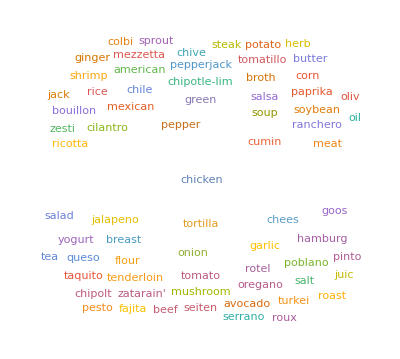

```mathematica
WordCloud[Select[Reverse[SortBy[Tally[Flatten[s]],Last]],MemberQ[EnchiladaIng,First[#]]&]]
```

Select only sentences that the word add in them, but take only the words that come after the word add.  At this moment we don’t care about substitution

```mathematica
Select[s,MemberQ[#,"add"]&]
result =Map[If[ListQ[FirstPosition[#,"add"] ],Part[#,FirstPosition[#,"add"][[1]]+1;;],Nothing]&,s];
(*result = Map[Sort[#]&,%]; *)
Tally[result];
```

Save result

```mathematica
DumpSave["OnlyAddResults.mx",result];
```

```mathematica
<< "OnlyAddResults.mx"
```

Concatenate words that form a 2-words ingredient

```mathematica
Concate2Words[l_]:=Module[{k,temp},temp = Map[If[SubsetQ[#,l],Position[#,l[[1]]|l[[2]]]]&,result];
Table[If[Length[temp[[i]]]== 2,k=Flatten[temp[[i]]];Print[temp[[i]]];If [Abs[k[[1]]-k[[2]]]==1,result[[i]] = ReplacePart[result[[i]],k[[1]]-> result[[i,k[[1]]]]<>" "<>result[[i,k[[2]]]]];
result[[i]]=ReplacePart[result[[i]],k[[2]]-> ""]]],{i,Length[temp]}]]
```

```mathematica
Map[Concate2Words[#]&,{{"chicken" , "broth"},{"green","onion"},{"rotel","tomato"},{"green", "pepper"},{"green","chili"},{"sour","cream"},{"taco","season"},{"spanish","rice"},{"black","oliv"}}];
```

```mathematica
result = Map[Sort[#]&,result];
```

Noticed “roux”, which is a mixture of flour, butter, and milk.  As these ingredients are already in the original recipe, we remove the word “roux”

```mathematica
result = result /. "roux" -> Nothing
```

```mathematica
DeleteDuplicates[Flatten[result]]
```

```mathematica
DumpSave["OnlyAddSentences.mx",result]
```

Keep only words in reviews but not in the original recipe

```mathematica
complementList =Complement[EnchiladaIng,IntheRecipe]
```

{american,avocado,beef,black oliv,bouillon,breast,chile,chipolt,chipotle-lim,chive,cilantro,colbi,corn,cornstartch,cumin,fajita,garlic,ginger,goos,green chili,green onion,green pepper,guacomol,hamburg,herb,jalapeno,jalapeños,juic,lettic,meat,mezzetta,mushroom,oliv,oregano,paprika,pepper,pepperjack,pesto,pinto,poblano,potato,queso,qusaddilla,ranchero,rice,ricotta,roast,rotel,rotel tomato,roux,salad,salsa,salt,seiten,serrano,shrimp,soup,soybean,spanish rice,sprout,steak,taco season,taquito,tea,tenderloin,tomatillo,tomato,turkei,yogurt,zatarain',zesti}

Perform a frequency count of the ingredients in the add recipes

```mathematica
Select[Flatten[result],MemberQ[complementList,#]&];
```

```mathematica
% /. "rotel" -> "rotel tomato"
t = Tally[%]
Length[t]
Select[t,Last[#] ≥ 2&]
sortedFreqCount = SortBy[%,Last]
```

{{bouillon,2},{oregano,2},{queso,2},{roast,2},{spanish rice,2},{fajita,3},{juic,3},{tomatillo,3},{yogurt,3},{black oliv,5},{rice,5},{meat,6},{corn,8},{cilantro,12},{tomato,13},{taco season,14},{salsa,17},{chile,18},{green chili,20},{jalapeno,22},{salt,24},{garlic,38},{rotel tomato,39},{pepper,45},{cumin,73}}

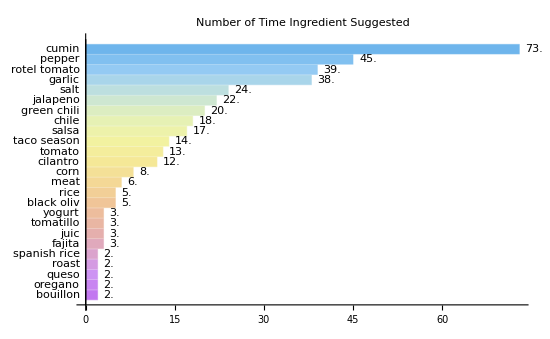

```mathematica
BarChart[N[sortedFreqCount [[All,2]],2.],BarOrigin->Left,ChartLabels->{Placed[sortedFreqCount [[All,1]],Before]},LabelingFunction->After,PlotLabel->"Number of Time Ingredient Suggested" ,ChartStyle->"Pastel",BarSpacing-> Automatic]
```

Perform a word cloud

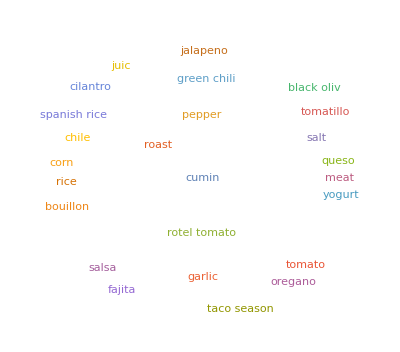

```mathematica
WordCloud[sortedFreqCount]
```

## Do A Graph Analysis

Here you can see how graph network can help to understand ingredients interaction in the reviews

```mathematica
intersectEnchilada =DeleteCases[ Map[Intersection[#,EnchiladaIng]&,result],{}];
```

```mathematica
f[re_List] :=Module[{flatTread,i,j},Flatten[Map[(Thread[#->#,#])&,re ]];
flatTread = Table[Thread[re[[i]]->  re[[j]]],{i,Length[re-1]},{j,i+1,Length[re]}];
flatTread = Flatten[flatTread];
UndirectedEdge @@@ flatTread]
```

```mathematica
cleanIntersection = DeleteCases[Map[f,intersectEnchilada],{}]
cleanIntersection = Flatten[cleanIntersection];
```

```mathematica
sg = Graph[cleanIntersection,{VertexLabels-> Placed ["Name",Center],EdgeStyle->RGBColor[0.5,0.8,0.5,0.10],VertexStyle-> Yellow
,VertexLabelStyle->Directive[FontFamily->"Arial",12,Bold,Purple]},GraphLayout->"SpringEmbedding"];
```

From the Community graph plot, you can see that ingredients that go together are tight together.  You can see that reviewer have added salt, pepper, cumin, and garlic to the chicken.  You also notice that tomato, taco seasoning, Rotel tomato are also in the same circle of friends

```mathematica
CommunityGraphPlot[sg,Method->"Hierarchical"]
```

-Graphics-